```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Regressive Näherung von Daten (Messdatenreihe oder diskretisierte Funktion) durch möglichst einfache periodische Funktion ϕ(x). Im folgenden Programm wird eine nach dem n-ten Glied abgebrochene Fourier-Reihe verwendet:

ϕ[x]=∑_(i=0)^n a_i·cos[i ω x]+b_i·sin[i ω x]

Es resultiert ein überbestimmtes Gleichungssystem, woraus sich folgende Bedingung ableiten lässt:

Anzahl  der Datenpunkte > Anzahl der Summanden von ϕ(x)

## Eingabe (𝒹𝒶𝓉ℯ𝓃)

```mathematica
ClearAll["Global`*"]
𝒹𝒶𝓉ℯ𝓃=Table[{x,Mod[x,2π]^2+RandomReal[.5]},{x,0,4π,π/20}];
```

## Plot

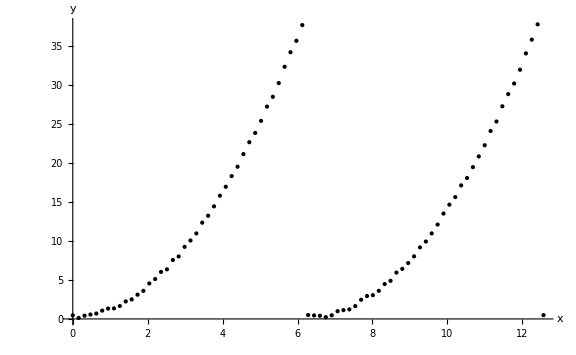

```mathematica
plotDaten=ListPlot[𝒹𝒶𝓉ℯ𝓃,
PlotStyle->{Black,PointSize->Medium},AxesLabel->{"x","y"},PlotRange->All,ImageSize->Large];
Print[Show[plotDaten]]
```

## Programm (automatisch)

```mathematica
n=3;
ω=1;
```

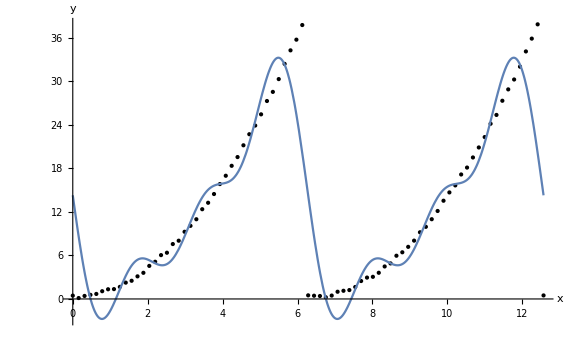

ϕ(x) = 12.7457+2.69222 Cos[x]-0.311103 Cos[2 x]-0.842144 Cos[3 x]-12.5709 Sin[x]-6.20056 Sin[2 x]-4.11122 Sin[3 x]
ρ = 4.79527

```mathematica
(*Programm*)
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃=Join[Table[Cos[i ω x],{i,0,n}],Table[Sin[i ω x],{i,0,n}]];
ϕ[x_]=Fit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃,x];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Print[Show[plotDaten,plot,PlotRange->All]]
Print[StringForm["ϕ(x) = ``\nρ = ``",ϕ[x],ρ]]
```

## Programm (manuell)

```mathematica
n=3;
ω=1;
```

```mathematica
(*Programm*)
𝒜1=Table[Cos[j ω 𝒹𝒶𝓉ℯ𝓃[[i,1]]],{i,Length[𝒹𝒶𝓉ℯ𝓃]},{j,0,n}];
𝒜2=Table[Sin[j ω 𝒹𝒶𝓉ℯ𝓃[[i,1]]],{i,Length[𝒹𝒶𝓉ℯ𝓃]},{j,0,n}];
𝒜=ArrayFlatten[{{𝒜1,𝒜2}}];
𝒷=𝒹𝒶𝓉ℯ𝓃[[All,2]];
𝒸=LeastSquares[𝒜,𝒷];
ϕ[x_]=Sum[𝒸[[i+1]]Cos[i ω x],{i,0,n}]+Sum[𝒸[[i+2+n]]Sin[i ω x],{i,0,n}];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Print[Show[plotDaten,plot,PlotRange->All]]
Print[StringForm["ϕ(x) = ``\nρ = ``",ϕ[x],ρ]]
```

-Graphics-

ϕ(x) = 12.7457+2.69222 Cos[x]-0.311103 Cos[2 x]-0.842144 Cos[3 x]-12.5709 Sin[x]-6.20056 Sin[2 x]-4.11122 Sin[3 x]
ρ = 4.79527

## Programm (Vergleich)

```mathematica
j=6;
ω=1;
```

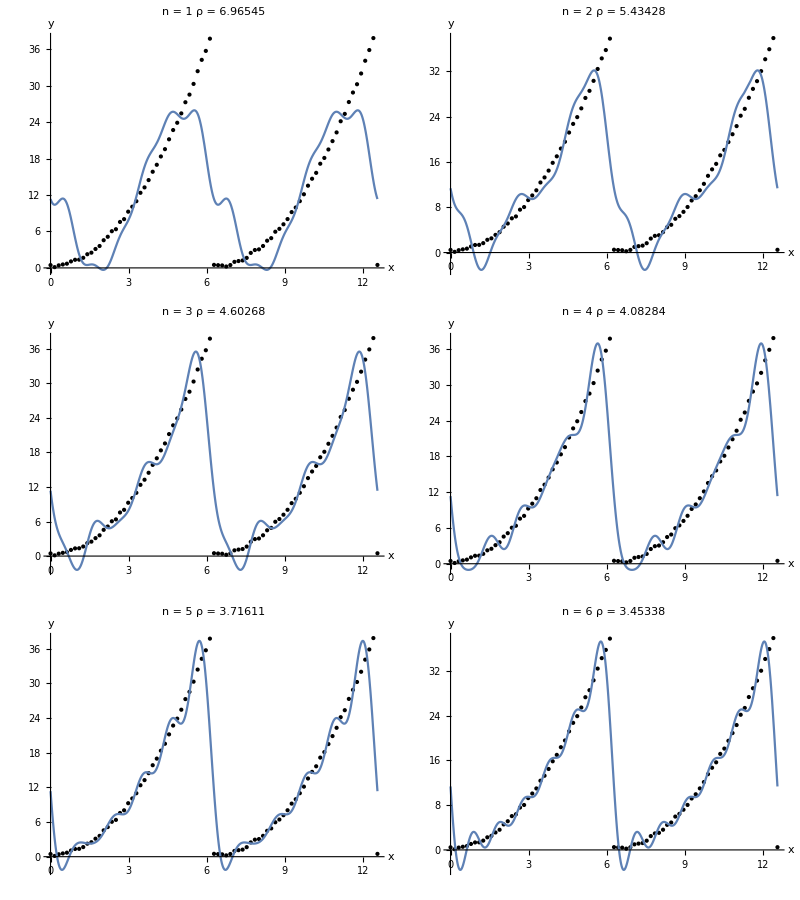

```mathematica
Print[TableForm[Partition[Table[
(*Programm*)
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃=Join[Table[Cos[i ω x],{i,0,j}],Table[Sin[i ω x],{i,0,j}]];
ϕ[x_]=Fit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃,x];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Show[plotDaten,plot,PlotRange->All,PlotLabel->StringForm["n = ``\nρ = ``",j,ρ],ImageSize->Medium]
,{j,If[Mod[n,2]==0,n,n+1]}],2]]]
```